## Úkol 1:

```mathematica
ST="BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF"
```

BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF

Na tomto grafu jde vidět “hluché” místo na písmenech i,j,k,l,m.
Angličtina má relativně takové místo přímo na j,k a dále na v,w,x.
Zkusil jsem vzdálenost čísla “J” od “W”, tj. 13, a to rozšifrovalo zprávu.

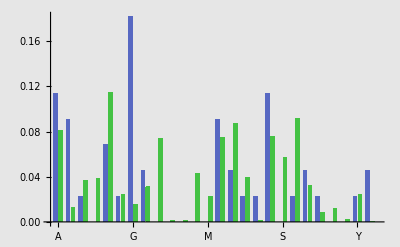

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

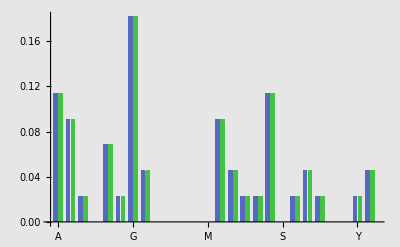

```mathematica
BEZGrafyRelCetnosti[ST,ST]
```

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

```mathematica
RelCetnosti[ST]
```

A
0.11 | B
0.091 | C
0.023 | D
0 | E
0.068 | F
0.023 | G
0.18
H
0.045 | I
0 | J
0 | K
0 | L
0 | M
0 | N
0.091
O
0.045 | P
0.023 | Q
0.023 | R
0.11 | S
0 | T
0.023 | U
0.045
V
0.023 | W
0 | X
0 | Y
0.023 | Z
0.045 |  |

```mathematica
(*Výsledek*)
Caesar[ST,-13]
```

ONTHEATTEMPTNUMBERTHREENOTBADCONGRATULATIONS

## Úkol 2:

```mathematica
ST="PGNUSNPGNUSNNRSFCTTINRCWNIHUIPNSFFEXNSBNRSFSWCAFSCNBSCHNGKGYSTSJGFSNRCNKCHHNRSJIFWNMINPSWWWCIBNRSQIPACPBNRSMRINSFCTTINTHSMNRFSSTHCWNWGPNRSNFEYXSNCPBKCHHSBGENJIFWNMINPSWWNRSJIFWNMINPSWWMCWNRSRCNNSFRSKCYSIPMINRCNSCKEXIPGPSRCPBCPBCXISKSGJTFSCBCPBTENNSFIPNRSGNRSFITSAXCFBGPUGEFYCZSWNURSTSACPJGFTFIPAIPANRSWSIPTENIRCBPNOEINSJIPIWRSBYUNSCMRSPIMCWWSPNJGFUGEGEARNNGRCVSJIPIWRSBWCIBNRSQIPAMRSPBIBUGETSAIPNRSRCNNSFHGGQSBCNNRSYCFKRRCFSMRGRCBJGHHGMSBRIYIPNGNRSKGEFNCFYIPCFYMINRNRSBGFYGEWSJGEFNSSPNRGJYCFKRINRIPQINMCWRSWCIBJIJNSSPNRWCIBNRSYCFKRRCFSWIDNSSPNRCBBSBNRSBGFYGEWSMFINSNRCNBGMPNRSQIPAWCIBNGNRSZEFUCPBNRSZEFUSCASFHUMFGNSBGMPCHHNRFSS";
```

Nyní proveďte analýzu četnosti:

```mathematica
RelCetnosti[ST]
```

A
0.018 | B
0.049 | C
0.08 | D
0.0016 | E
0.027 | F
0.062 | G
0.056
H
0.022 | I
0.075 | J
0.022 | K
0.016 | L
0 | M
0.029 | N
0.13
O
0.0016 | P
0.064 | Q
0.008 | R
0.086 | S
0.13 | T
0.022 | U
0.018
V
0.0016 | W
0.046 | X
0.008 | Y
0.021 | Z
0.0048 |  |

A srovnejte ji s četnostmi pro angličtinu:

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

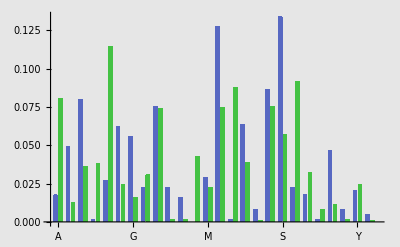

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

Na grafu je patrné, že dvě nejčastější písmena ŠT jsou S, N.
Nejčastější písmena v angličtině jsou E,T a proto jsem je na sebe namapoval v této afinní substituci.

```mathematica
s=Solve[{
Pozice["S"]==cc*Pozice["E"]+dd,
Pozice["N"]==cc*Pozice["T"]+dd
}, Modulus->NCharacters]
{c,d}={cc,dd}/.s[[1]]
AXPBDecrypt[ST,c,d]
```

{{dd→2,cc→17}}

{17,2}

```mathematica
(*Výsledek*)
```

NOTYETNOTYETTHERABBITHASTILYINTERRUPTEDTHERESAGREATDEALTOCOMEBEFORETHATCALLTHEFIRSTWITNESSSAIDTHEKINGANDTHEWHITERABBITBLEWTHREEBLASTSONTHETRUMPETANDCALLEDOUTFIRSTWITNESSTHEFIRSTWITNESSWASTHEHATTERHECAMEINWITHATEACUPINONEHANDANDAPIECEOFBREADANDBUTTERINTHEOTHERIBEGPARDONYOURMAJESTYHEBEGANFORBRINGINGTHESEINBUTIHADNTQUITEFINISHEDMYTEAWHENIWASSENTFORYOUOUGHTTOHAVEFINISHEDSAIDTHEKINGWHENDIDYOUBEGINTHEHATTERLOOKEDATTHEMARCHHAREWHOHADFOLLOWEDHIMINTOTHECOURTARMINARMWITHTHEDORMOUSEFOURTEENTHOFMARCHITHINKITWASHESAIDFIFTEENTHSAIDTHEMARCHHARESIXTEENTHADDEDTHEDORMOUSEWRITETHATDOWNTHEKINGSAIDTOTHEJURYANDTHEJURYEAGERLYWROTEDOWNALLTHREE

## Úkol 3:

```mathematica
ST="AWEWRTFELADHAAUDITTIBSMXCCHTBHBXEHEEIELX"
```

AWEWRTFELADHAAUDITTIBSMXCCHTBHBXEHEEIELX

Nyní se snažte zjistit, jakou transpozici váš soused použil. Využijte metod popsaných na minulém slajdu. Pro jednoduchost faktorizaci opakujeme nyní pro proměnnou šifrového textu:

```mathematica
FactorInteger[StringLength[ST]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^3,5^1}

Všiml jsem si paddingu X, které mi text rozdělilo na řádky dlouhé 8 písmen a také číslo 8 dělí počet písmen v ŠT:

```mathematica
(*
AWEWRTFE
LADHAAUD
ITTIBSMX
CCHTBHBX
EHEEIELX
*)
```

```mathematica
(*Výsledek*)
```

```mathematica
Transpozice[ST,8]
```

ALICEWATCHEDTHEWHITERABBITASHEFUMBLEDXXX